```mathematica
Clear["Global`*"]
```

```mathematica
gamma = 1/10
```

1/10

```mathematica
eta= 1
```

1

```mathematica
delta = 1/4
```

1/4

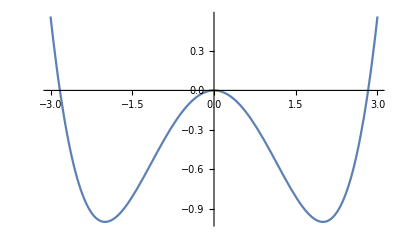

```mathematica
Plot[-1/2*eta*x^2 + delta * (x^4)/4, {x, -3, 3}]
```

```mathematica
DE:={x'[t]==y[t], y'[t]==-gamma*y[t]+eta*x[t]-delta*x[t]^3,x[0]==3, y[0]==10}
```

```mathematica
sol=NDSolve[DE,{x, y}, {t,0,100}]
```

{{x→InterpolatingFunction[{{0., 100.}}, <>],y→InterpolatingFunction[{{0., 100.}}, <>]}}

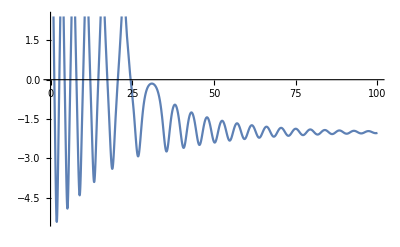

```mathematica
Plot[Evaluate[x[t]/.sol], {t,0,100}]
```

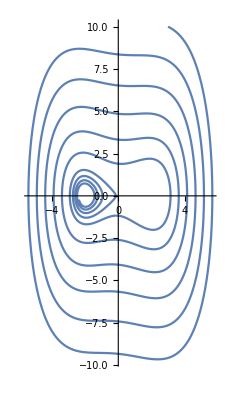

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,50}]
```

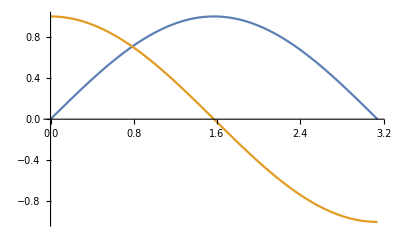

```mathematica
Plot[{Sin[x],Cos[x]}, {x,0,Pi}]
```

```mathematica
X[t_]:=Evaluate[x[t]/.sol]
```

```mathematica
X[1]
```

{1.47103}

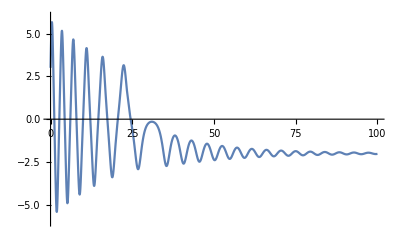

```mathematica
Plot[X[t],{t,0,100}, PlotRange->{-6,6}]
```

```mathematica
D[u[x,t],{t,2}]
```

u^(0,2)[x,t]

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n. 
D[f,x,y,…] differentiates f successively with respect to x,y,….
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives a tensor derivative.

```mathematica
Sum[i, {i,1,100,3}]
```

1717

```mathematica
Product[i,{i,1,10}]
```

3628800

```mathematica
Product[i,{i,1,10,2}]
```

945

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

```mathematica
?assume
```

Information::notfound: Symbol "assume" not found.

```mathematica
Solve[x^2==a,x]
```

{{x→-√a},{x→√a}}

```mathematica
x/.{{x->-√a},{x->√a}}
```

{-√a,√a}

```mathematica
Assuming[a>0,Solve[x^2==a,x]]
```

{{x→-√a},{x→√a}}

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

```mathematica
Solve[Sin[x]==0,x]
```

{{x→ConditionalExpression[2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

```mathematica
First[{{x->ConditionalExpression[2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}]
```

{x→ConditionalExpression[2 π C[1],C[1]∈Integers]}